# CaffeLink

## MNIST example

## Requirements and Initialization

This example shows how to use CaffeLink to build, train and test LeNet. It relies on examples from Caffe, which can be found here.
Except for successfully build Caffe and CaffeLink, for this example MNIST data are also needed. Those can be obtained using script from Caffe:

  cd $CAFFE_ROOT
 ./data/mnist/get_mnist.sh
 ./examples/mnist/create_mnist.sh
 
As is shown in MNIST example on Caffe web. This document is only concerned with CaffeLink, so for details regarding net design please refer to Caffe.

Caffe is a command line tool and it would be inefficient to somehow transmit all its output to Mathematica. So it is highly recommended to launch Mathematica session with terminal. CaffeLink also relies on stoud.

### Initialize CaffeLink

The first think to do is load CaffeLink module and initialize it with path to caffe.proto protobuffer definition of all parameters Caffe uses.

```mathematica
Needs["CaffeLink`",FileNameJoin[{NotebookDirectory[],"..","caffeLink.m"}]];
InitCaffeLinkModule["fel-lin/caffe/src/caffe/proto/caffe.proto"];
```

Before training, testing etc. CaffeLink library must be initialized. That is: choose data type (double or float), computing mode (GPU or CPU) and device ID for GPU mode.

```mathematica
initCaffeLink[True,True,0]
```

Mode can be switched later, data type not.

## Net

### Building

A net is represented by its proto file. Path to or content of LeNet proto lenet_train_test.prototxt could be directly passed to CaffeLink, but it would be no fun. Functions NewNet, AddLayer, SetNetParam and SetLayerParam allow to gradually build the net. GetNetParamString then produces protobuffer string which is used to create net in CaffeLink.

This path should point to your mnist data set. Absolute path is recommended.

```mathematica
mnistPath="/home/kerhy/fel-lin/caffe/examples/mnist/";
```

#### Build LeNet

```mathematica
net=NewNet["LeNet"];
li=0;
```

```mathematica
li++;
net=AddLayer[net,"DATA","mnist"];
net=SetLayerParam[net,li,"top",{"data","label"}];
net=SetLayerParam[net,li,"source",StringJoin[mnistPath,"mnist_train_lmdb"]];
net=SetLayerParam[net,li,"backend","LMDB"];
net=SetLayerParam[net,li,"batch_size",64];
net=SetLayerParam[net,li,"scale",0.00390625];
net=SetLayerParam[net,li,"include.phase","TRAIN"];
```

```mathematica
li++;
net=AddLayer[net,"DATA","mnist"];
net=SetLayerParam[net,li,"top",{"data","label"}];
net=SetLayerParam[net,li,"source",StringJoin[mnistPath,"mnist_train_lmdb"]];
net=SetLayerParam[net,li,"backend","LMDB"];
net=SetLayerParam[net,li,"batch_size",64];
net=SetLayerParam[net,li,"scale",0.00390625];
net=SetLayerParam[net,li,"include.phase","TEST"];
```

```mathematica
li++;
net=AddLayer[net,"CONVOLUTION","conv1"];
net=SetLayerParam[net,li,"bottom","data"];
net=SetLayerParam[net,li,"top","conv1"];
net=SetLayerParam[net,li,"blobs_lr",{1,2}];
net=SetLayerParam[net,li,"num_output",20];
net=SetLayerParam[net,li,"kernel_size",5];
net=SetLayerParam[net,li,"stride",1];
net=SetLayerParam[net,li,"weight_filler.type","xavier"];
net=SetLayerParam[net,li,"bias_filler.type","constant"];
```

```mathematica
li++;
net=AddLayer[net,"POOLING","pool1"];
net=SetLayerParam[net,li,"bottom","conv1"];
net=SetLayerParam[net,li,"top","pool1"];
net=SetLayerParam[net,li,"pool","MAX"];
net=SetLayerParam[net,li,"kernel_size",2];
net=SetLayerParam[net,li,"stride",2];
```

```mathematica
li++;
net=AddLayer[net,"CONVOLUTION","conv2"];
net=SetLayerParam[net,li,"bottom","pool1"];
net=SetLayerParam[net,li,"top","conv2"];
net=SetLayerParam[net,li,"blobs_lr",{1,2}];
net=SetLayerParam[net,li,"num_output",50];
net=SetLayerParam[net,li,"kernel_size",5];
net=SetLayerParam[net,li,"stride",1];
net=SetLayerParam[net,li,"weight_filler.type","xavier"];
net=SetLayerParam[net,li,"bias_filler.type","constant"];
```

```mathematica
li++;
net=AddLayer[net,"POOLING","pool2"];
net=SetLayerParam[net,li,"bottom","conv2"];
net=SetLayerParam[net,li,"top","pool2"];
net=SetLayerParam[net,li,"pool","MAX"];
net=SetLayerParam[net,li,"kernel_size",2];
net=SetLayerParam[net,li,"stride",2];
```

```mathematica
li++;
net=AddLayer[net,"INNER_PRODUCT","ip1"];
net=SetLayerParam[net,li,"bottom","pool2"];
net=SetLayerParam[net,li,"top","ip1"];
net=SetLayerParam[net,li,"blobs_lr",{1,2}];
net=SetLayerParam[net,li,"num_output",500];
net=SetLayerParam[net,li,"weight_filler.type","xavier"];
net=SetLayerParam[net,li,"bias_filler.type","constant"];
```

```mathematica
li++;
net=AddLayer[net,"RELU","relu1"];
net=SetLayerParam[net,li,"bottom","ip1"];
net=SetLayerParam[net,li,"top","ip1"];
```

```mathematica
li++;
net=AddLayer[net,"INNER_PRODUCT","ip2"];
net=SetLayerParam[net,li,"bottom","ip1"];
net=SetLayerParam[net,li,"top","ip2"];
net=SetLayerParam[net,li,"blobs_lr",{1,2}];
net=SetLayerParam[net,li,"num_output",10];
net=SetLayerParam[net,li,"weight_filler.type","xavier"];
net=SetLayerParam[net,li,"bias_filler.type","constant"];
```

```mathematica
li++;
net=AddLayer[net,"ACCURACY","accuracy"];
net=SetLayerParam[net,li,"bottom",{"ip2","label"}];
net=SetLayerParam[net,li,"top","accuracy"];
net=SetLayerParam[net,li,"include.phase","TEST"];
```

```mathematica
li++;
net=AddLayer[net,"SOFTMAX_LOSS","loss"];
net=SetLayerParam[net,li,"bottom",{"ip2","label"}];
net=SetLayerParam[net,li,"top","loss"];
```

Resulting string is equal to content of lenet_train_test.prototxt.

```mathematica
netParam=GetNetParamString[net]
```

name: "LeNet"
layers {
  top: "data"
  top: "label"
  name: "mnist"
  type: DATA
  include {
    phase: TRAIN
  }
  transform_param {
    scale: 0.00390625
  }
  data_param {
    source: "/home/kerhy/fel-lin/caffe/examples/mnist/mnist_train_lmdb"
    batch_size: 64
    backend: LMDB
  }
}
layers {
  top: "data"
  top: "label"
  name: "mnist"
  type: DATA
  include {
    phase: TEST
  }
  transform_param {
    scale: 0.00390625
  }
  data_param {
    source: "/home/kerhy/fel-lin/caffe/examples/mnist/mnist_train_lmdb"
    batch_size: 64
    backend: LMDB
  }
}
layers {
  bottom: "data"
  top: "conv1"
  name: "conv1"
  type: CONVOLUTION
  blobs_lr: 1
  blobs_lr: 2
  convolution_param {
    num_output: 20
    kernel_size: 5
    stride: 1
    weight_filler {
      type: "xavier"
    }
    bias_filler {
      type: "constant"
    }
  }
}
layers {
  bottom: "conv1"
  top: "pool1"
  name: "pool1"
  type: POOLING
  pooling_param {
    pool: MAX
    kernel_size: 2
    stride: 2
  }
}
layers {
  bottom: "pool1"
  top: "conv2"
  name: "conv2"
  type: CONVOLUTION
  blobs_lr: 1
  blobs_lr: 2
  convolution_param {
    num_output: 50
    kernel_size: 5
    stride: 1
    weight_filler {
      type: "xavier"
    }
    bias_filler {
      type: "constant"
    }
  }
}
layers {
  bottom: "conv2"
  top: "pool2"
  name: "pool2"
  type: POOLING
  pooling_param {
    pool: MAX
    kernel_size: 2
    stride: 2
  }
}
layers {
  bottom: "pool2"
  top: "ip1"
  name: "ip1"
  type: INNER_PRODUCT
  blobs_lr: 1
  blobs_lr: 2
  inner_product_param {
    num_output: 500
    weight_filler {
      type: "xavier"
    }
    bias_filler {
      type: "constant"
    }
  }
}
layers {
  bottom: "ip1"
  top: "ip1"
  name: "relu1"
  type: RELU
}
layers {
  bottom: "ip1"
  top: "ip2"
  name: "ip2"
  type: INNER_PRODUCT
  blobs_lr: 1
  blobs_lr: 2
  inner_product_param {
    num_output: 10
    weight_filler {
      type: "xavier"
    }
    bias_filler {
      type: "constant"
    }
  }
}
layers {
  bottom: "ip2"
  bottom: "label"
  top: "accuracy"
  name: "accuracy"
  type: ACCURACY
  include {
    phase: TEST
  }
}
layers {
  bottom: "ip2"
  bottom: "label"
  top: "loss"
  name: "loss"
  type: SOFTMAX_LOSS
}

For now, CaffeLink supports net definition in solver only via path to protobuffer file, so it must be saved.

```mathematica
Export[StringJoin[NotebookDirectory[],"lenet.proto"],netParam,"Text"]
```

/home/kerhy/fel-lin/mthmt/lenet.proto

#### Notes:

Repeating parameters can be set with array:
  net=SetLayerParam[net,li,”top”,{“data”,”label”}];
resulting in:
  top: “data”
 top: “label”

Parameters with the same name but in different block must be specified with the block name as well:
  net=SetLayerParam[net,li,”weight_filler.type”,”xavier”];
 net=SetLayerParam[net,li,”bias_filler.type”,”constant”];
gives:
 weight_filler {
 	type: “xavier”
 }
 bias_filler {
 	type: “constant”
 }
This holds even if only one of these is used.

### Training

Before training a solver must be defined. This can be done in a similar way to building net, or an existing file can be used.

#### Define solver

```mathematica
solver=NewSolver["SGD"];
solver=SetSolverParam[solver,"net",StringJoin[NotebookDirectory[],"lenet.proto"]];
solver=SetSolverParam[solver,"test_iter",100];
solver=SetSolverParam[solver,"test_interval",500];
solver=SetSolverParam[solver,"base_lr",0.01];
solver=SetSolverParam[solver,"momentum",0.9];
solver=SetSolverParam[solver,"weight_decay",0.0005];
solver=SetSolverParam[solver,"lr_policy","inv"];
solver=SetSolverParam[solver,"gamma",0.0001];
solver=SetSolverParam[solver,"power",0.75];solver=SetSolverParam[solver,"display",100];
solver=SetSolverParam[solver,"max_iter",1000];
solver=SetSolverParam[solver,"snapshot",1000];
solver=SetSolverParam[solver,"snapshot_prefix",StringJoin[NotebookDirectory[],"snaps/lenet"]];
solver=SetSolverParam[solver,"solver_mode","GPU"];

solveParam=GetNetParamString[solver]
```

net: "/home/kerhy/fel-lin/mthmt/lenet.proto"
test_iter: 100
test_interval: 500
base_lr: 0.01
display: 100
max_iter: 1000
lr_policy: "inv"
gamma: 0.0001
power: 0.75
momentum: 0.9
weight_decay: 0.0005
snapshot: 1000
snapshot_prefix: "/home/kerhy/fel-lin/mthmt/snaps/lenet"
solver_mode: GPU
solver_type: SGD

#### Notes

Create snapshot directory:

```mathematica
CreateDirectory[StringJoin[NotebookDirectory[],"snaps/"]]
```

Either double check relative paths or simply use absolute. All directories must exist. Be careful especially with source path in DATA layers. Current working directory can be printed in console with printWorkingPath.

```mathematica
printWorkingPath[]
```

#### Train LeNet

New net can be trained with functions trainNetString and trainNetFile. The first expects solver parameters in a string, the second expects path pointing to a file with parameters. Both do the same. Training progress is printed to console.

```mathematica
trainNetString[solveParam]
```

### Testing

Net testing requires a net and net parameters, referred by Caffe as deploy proto. The main difference between deploy and training proto is in input definition, the rest can be the same.

#### Deploy LeNet

```mathematica
net=NewNet["LeNet - deploy"];
net=SetNetParam[net,"input","data"];
net=SetNetParam[net,"input_dim",{10,1,28,28}];
li=0;
```

```mathematica
li++;
net=AddLayer[net,"CONVOLUTION","conv1"];
net=SetLayerParam[net,li,"bottom","data"];
net=SetLayerParam[net,li,"top","conv1"];
net=SetLayerParam[net,li,"blobs_lr",{1,2}];
net=SetLayerParam[net,li,"num_output",20];
net=SetLayerParam[net,li,"kernel_size",5];
net=SetLayerParam[net,li,"stride",1];
net=SetLayerParam[net,li,"weight_filler.type","xavier"];
net=SetLayerParam[net,li,"bias_filler.type","constant"];
```

```mathematica
li++;
net=AddLayer[net,"POOLING","pool1"];
net=SetLayerParam[net,li,"bottom","conv1"];
net=SetLayerParam[net,li,"top","pool1"];
net=SetLayerParam[net,li,"pool","MAX"];
net=SetLayerParam[net,li,"kernel_size",2];
net=SetLayerParam[net,li,"stride",2];
```

```mathematica
li++;
net=AddLayer[net,"CONVOLUTION","conv2"];
net=SetLayerParam[net,li,"bottom","pool1"];
net=SetLayerParam[net,li,"top","conv2"];
net=SetLayerParam[net,li,"blobs_lr",{1,2}];
net=SetLayerParam[net,li,"num_output",50];
net=SetLayerParam[net,li,"kernel_size",5];
net=SetLayerParam[net,li,"stride",1];
net=SetLayerParam[net,li,"weight_filler.type","xavier"];
net=SetLayerParam[net,li,"bias_filler.type","constant"];
```

```mathematica
li++;
net=AddLayer[net,"POOLING","pool2"];
net=SetLayerParam[net,li,"bottom","conv2"];
net=SetLayerParam[net,li,"top","pool2"];
net=SetLayerParam[net,li,"pool","MAX"];
net=SetLayerParam[net,li,"kernel_size",2];
net=SetLayerParam[net,li,"stride",2];
```

```mathematica
li++;
net=AddLayer[net,"INNER_PRODUCT","ip1"];
net=SetLayerParam[net,li,"bottom","pool2"];
net=SetLayerParam[net,li,"top","ip1"];
net=SetLayerParam[net,li,"blobs_lr",{1,2}];
net=SetLayerParam[net,li,"num_output",500];
net=SetLayerParam[net,li,"weight_filler.type","xavier"];
net=SetLayerParam[net,li,"bias_filler.type","constant"];
```

```mathematica
li++;
net=AddLayer[net,"RELU","relu1"];
net=SetLayerParam[net,li,"bottom","ip1"];
net=SetLayerParam[net,li,"top","ip1"];
```

```mathematica
li++;
net=AddLayer[net,"INNER_PRODUCT","ip2"];
net=SetLayerParam[net,li,"bottom","ip1"];
net=SetLayerParam[net,li,"top","ip2"];
net=SetLayerParam[net,li,"blobs_lr",{1,2}];
net=SetLayerParam[net,li,"num_output",10];
net=SetLayerParam[net,li,"weight_filler.type","xavier"];
net=SetLayerParam[net,li,"bias_filler.type","constant"];
```

```mathematica
li++;
net=AddLayer[net,"SOFTMAX","prob"];
net=SetLayerParam[net,li,"bottom","ip2"];
net=SetLayerParam[net,li,"top","prob"];
```

```mathematica
netDeploy=GetNetParamString[net]
```

name: "LeNet - deploy"
input: "data"
input_dim: 10
input_dim: 1
input_dim: 28
input_dim: 28
layers {
  bottom: "data"
  top: "conv1"
  name: "conv1"
  type: CONVOLUTION
  blobs_lr: 1
  blobs_lr: 2
  convolution_param {
    num_output: 20
    kernel_size: 5
    stride: 1
    weight_filler {
      type: "xavier"
    }
    bias_filler {
      type: "constant"
    }
  }
}
layers {
  bottom: "conv1"
  top: "pool1"
  name: "pool1"
  type: POOLING
  pooling_param {
    pool: MAX
    kernel_size: 2
    stride: 2
  }
}
layers {
  bottom: "pool1"
  top: "conv2"
  name: "conv2"
  type: CONVOLUTION
  blobs_lr: 1
  blobs_lr: 2
  convolution_param {
    num_output: 50
    kernel_size: 5
    stride: 1
    weight_filler {
      type: "xavier"
    }
    bias_filler {
      type: "constant"
    }
  }
}
layers {
  bottom: "conv2"
  top: "pool2"
  name: "pool2"
  type: POOLING
  pooling_param {
    pool: MAX
    kernel_size: 2
    stride: 2
  }
}
layers {
  bottom: "pool2"
  top: "ip1"
  name: "ip1"
  type: INNER_PRODUCT
  blobs_lr: 1
  blobs_lr: 2
  inner_product_param {
    num_output: 500
    weight_filler {
      type: "xavier"
    }
    bias_filler {
      type: "constant"
    }
  }
}
layers {
  bottom: "ip1"
  top: "ip1"
  name: "relu1"
  type: RELU
}
layers {
  bottom: "ip1"
  top: "ip2"
  name: "ip2"
  type: INNER_PRODUCT
  blobs_lr: 1
  blobs_lr: 2
  inner_product_param {
    num_output: 10
    weight_filler {
      type: "xavier"
    }
    bias_filler {
      type: "constant"
    }
  }
}
layers {
  bottom: "ip2"
  top: "prob"
  name: "prob"
  type: SOFTMAX
}

#### Test LeNet

Tested net must be prepared at first. Caffe allocates memory and creates net topology based on given deploy proto. Preparation is done either from string with prepareNetString or from file path using prepareNetFile.

```mathematica
prepareNetString[netDeploy]
```

Net info can be printed (to console) with printNetInfo.

```mathematica
printNetInfo[]
```

After preparation, any net data with the same topology can be loaded.

```mathematica
loadNet[StringJoin[NotebookDirectory[],"snaps/lenet_iter_1000.caffemodel"]]
```

That also allows extracting learned parameters (weights, filters, etc.).

Insertion of data to be tested is necessary only if there is no DATA layer in the deploy proto.

```mathematica
inputImgs={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
input=Flatten[Map[ImageData[#]&,inputImgs,1]];
```

```mathematica
setInput[input]
```

This runs the test.

```mathematica
testNet[]
```

Result can be obtained from top blob of the last layer.

```mathematica
result=getTopBlob[7,0];
```

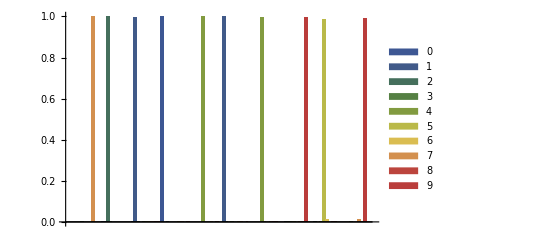

```mathematica
res=ArrayReshape[result,{10,10}];
leg={0,1,2,3,4,5,6,7,8,9};
BarChart[res,ChartLegends->leg,ChartStyle->"DarkRainbow"]
resList=Map[BarChart[#,ChartStyle->"DarkRainbow",ChartLabels->leg]&,res,1];
resList=ArrayReshape[Riffle[resList,inputImgs],{10,2}];
```

```mathematica
ListAnimate[resList,0.25]
```

### Fine tuning

For fine tuning, functions trainNetWeightsString or trainNetWeightsFile can be used. These two functions takes solver parameters from string or file and start training a new net with weights initialized from given net data.

```mathematica
trainNetWeightsString[solveParam,StringJoin[NotebookDirectory[],"snaps/lenet_iter_1000.caffemodel"]]
```

### Extracting features and net surgery

Functions getParamBlob, getTopBlob and getBottomBlob allow inspection of all blobs in net. In combination with setParamBlob weights can be easily copied to another layer or to completely different net.

As shown in test section, this loads net, inserts input and tests it.

```mathematica
prepareNetString[netDeploy]
loadNet[StringJoin[NotebookDirectory[],"snaps/lenet_iter_10000.caffemodel"]]
setInput[input]
testNet[]
printNetInfo[]
```

#### Surgery

For example, copying filters from layer conv1 to conv2 can be done like this:

```mathematica
filters=getParamBlob[0,0]; (* 0th layer: conv1, 0th par. blob - filters, 20x1x5x5 *)
filters2=getParamBlob[2,0];(* 2th layer: conv2, 0th par. blob - filters, 50x20x5x5 *)
filters2[[1;;Length[filters]]]=filters;
setParamBlob[filters2,2,0];
```

Now each of 20 channels in the first filter of conv2 is the same as one of 20 filters in conv1.
That could of course breaks the whole net. Anyway, altered net can be exported back to Caffe format with exportNet.

```mathematica
exportNet[StringJoin[NotebookDirectory[],"snaps/lenet_edited.caffemodel"]]
```

#### Visualization

In short: get parameters, separate and reshape them and then render.

Layer conv1 - filters

```mathematica
par=getParamBlob[0,0]; (* 0th layer: conv1, 0th par. blob - filters *)
```

```mathematica
filters=ArrayReshape[par,{20,5,5}]; (* conv1 has 20 filters, 5x5 *)
fImgs=Map[Image[#,Magnification->5]&,filters,1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Mapping image data to range 0,1 might be useful.

```mathematica
filters=Map[(#-Min[#])/(Max[#]-Min[#])&,filters,1];
fImgs=Map[Image[#,Magnification->5]&,filters,1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Layer conv1 - features

```mathematica
in=getBottomBlob[0,0];
out=getTopBlob[0,0];
```

This shows one input image and result after convolution (20 filters).

```mathematica
imgi=1; (* test image index, 1 - 10 *)
inImg=ArrayReshape[in,{10,28,28}][[imgi]];
outImgs=ArrayReshape[out,{10,20,24,24}][[imgi]];
{Image[inImg,Magnification->2],
Map[Image[#,Magnification->2]&,outImgs,1]}
```

{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

The same in range 0, 1 :

```mathematica
outImgs=Map[(#-Min[#])/(Max[#]-Min[#])&,outImgs,1];
{Image[inImg,Magnification->2],
Map[Image[#,Magnification->2]&,outImgs,1]}
```

{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

Layer conv2 - filters

```mathematica
par=getParamBlob[2,0]; (* 2th layer: conv2, 0th par. blob - filters *)
```

This show 20 channels of the first filter.

```mathematica
filters=ArrayReshape[par,{20,5,5}]; (* conv2 has 50 filterst with 20 channels each, 5x5 *)
Map[Image[#,Magnification->5]&,filters,1]
filters=Map[(#-Min[#])/(Max[#]-Min[#])&,filters,1];
Map[Image[#,Magnification->5]&,filters,1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Layer conv2 - features

```mathematica
in=getBottomBlob[2,0];
out=getTopBlob[2,0];
```

This shows one input image and result after convolution (50 filters).

```mathematica
imgi=1; (* test image index, 1 - 10 *)
imgfi=3; (* conv1 filter index, 1 - 20 *)
inImg=ArrayReshape[in,{10,20,12,12}][[imgi,imgfi]];
outImgs=ArrayReshape[out,{10,50,8,8}][[imgi]];
{Image[inImg,Magnification->4],
Map[Image[#,Magnification->4]&,outImgs,1]}
```

{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

The same in range 0, 1 :

```mathematica
outImgs=Map[(#-Min[#])/(Max[#]-Min[#])&,outImgs,1];
inImg=Map[(#-Min[#])/(Max[#]-Min[#])&,{inImg},1][[1]];
{Image[inImg,Magnification->4],
Map[Image[#,Magnification->4]&,outImgs,1]}
```

{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}